```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

x::shdw: Symbol x appears in multiple contexts {SSSiCv100`,Global`}; definitions in context SSSiCv100` may shadow or be shadowed by other definitions.

y::shdw: Symbol y appears in multiple contexts {SSSiCv100`,Global`}; definitions in context SSSiCv100` may shadow or be shadowed by other definitions.

w::shdw: Symbol w appears in multiple contexts {SSSiCv100`,Global`}; definitions in context SSSiCv100` may shadow or be shadowed by other definitions.

### Newer code: prepIC, unprepIC, RepsLen

Function to calculate Repetitions & Lengths:

```mathematica
prepIC[x_]:=Replace[x,IndexedConcatenate[y__,iter_]:>ic[y,iterator[Sequence@@Flatten[{iter}]]],All]
```

```mathematica
unprepIC[x_]:=Replace[x,ic[y__,z_iterator]:>IndexedConcatenate[y,If[Length[z]==1,First[z],List@@z]],All]
```

```mathematica
Clear[PSCSLengths];
PSCSLengths[l0_List] := Module[{l=prepIC[l0]},
If[FreeQ[l,List,{2,∞}],
If[$debug,Print[unprepIC[l],": ",{0,1}]];{0,1},
PSCSLengths /@ l]  (* non-nested list gets {0,1}, otherwise Thread it *)
];
(* CAUTION: use prepIC first, otherwise I-Cat iterators will be grabbed, too! *)

PSCSLengths[ic:_IndexedConcatenate]:=PSCSLengths[prepIC[ic]];

PSCSLengths[ic:ic[x__,iter_iterator]]:=Module[{argList={x},ans},
ans={ 
(*  len  *) Dot@@Transpose[LenAndReps /@ argList], (* No longer multiplying reps&len pairs! *)

(* reps *)  If[Length[iter]==3,iter[[-1]]-iter[[-2]]+1,(* else *) Last@iter ]
};
If[$debug,Print[unprepIC[ic],": ",ans]];
ans
];
```

```mathematica
Inner[Times,l1,l2,Plus]
```

```mathematica
Sum[i,{i,1,1}]
```

1

```mathematica
Sum[1,{i,1,0}]
```

0

```mathematica
Clear[vtxNum];
vtxNum[ic_,posEDS:{__Integer}]:=Module[{posICs=Most@posEDS,ans=Last@posEDS,icT,repsT,lenT,iterT},
(* The position of the EDS identifies positions of any nested I-Cats, the last element is the position of the EDS within the innermost I-Cat. 
We assume all iterators are already fully expanded: {var,start,stop} rather than {var,stop} or just stop *)
If[$debug,Print["ic: ",ic,", posEDS: ",posEDS,", posICs: ",posICs,", ans: ",ans]];
While[Length[posICs]>0,
icT=Extract[ic,posICs];
If[$debug,Print["pos: ",posICs,", icT: ",icT]];
{repsT,lenT}=RepsLen[icT];
iterT=Last@icT;
If[$debug,Print["reps: ",repsT,", len: ",lenT,", var-start: ",(iterT[[1]]-iterT[[2]])]];
ans=ans+lenT*(iterT[[1]]-iterT[[2]]); (* length * (variable - start), for this I-Cat *)
If[$debug,Print["ans: ",ans]];
While[Last[posICs]>1, (* does anything precede this innermost I-Cat? *)
posICs[[-1]]--;
If[$debug,Print["preceding term: ",Extract[ic,posICs],", full length: ",Times@@RepsLen[Extract[ic,posICs]]]];
ans = ans + Times@@RepsLen[Extract[ic,posICs]]; (* add in full length of preceding stuff *)
];
posICs=Drop[posICs,-1]; (* up one level, and we'll repeat for remaining nested I-Cats *)
];
ans
];
fullEdge[ic_,posEDS:{__Integer}]:=Module[{v=vtxNum[ic,posEDS],EDS=Extract[ic,posEDS ],old$debug=$debug},
$debug=True;
If[$debug,Print["ic: ",ic,"\n posEDS: ",posEDS,"\n v = ",v,"\n EDS: ",EDS]];
If[$debug,Print[Column[Rule[v,v+#]& /@ EDS]]];
$debug=old$debug;
ReplacePart[ic,posEDS->(Rule[v,v+#]& /@ EDS)]
];
```

### Try it on ICN Paper Examples

### Figure 5a

```mathematica
IC2a={IndexedConcatenate[{1},10]}
```

{€^10[{1}]}

```mathematica
IC2ap={IndexedConcatenate[{1},{i,1,10}]}
```

{€_(i⊨1)^10[{1}]}

```mathematica
{{Vertex #, , , (i-1)+1, , }, {position, , 1, 1,1, , }, {I-Cat, {, €_(i⊨1)^10[, {1}, ], }}, {pos:reps(len), , 1:∑_(i=1)^ℕ (1)=ℕ, , , }, {, , , 1, ↖, }}
```

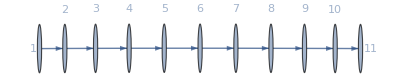

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Test RepsLen, Positions of Lists

```mathematica
RepsLen[IC2a]
```

{{10,1}}

```mathematica
{$debug=True,RepsLen[IC2a],$debug=False}[[2]]
```

{1}: {1,1}

€^10[{1}]: {10,1}

{{10,1}}

```mathematica
First[Most /@ Rest[Position[prepIC[IC2a],List]]]
```

{1,1}

```mathematica
vtxNum[IC2ap,{1,1}]
```

i

```mathematica
Most /@ Rest[Position[prepIC[IC2ap],List]]
```

{{1,1}}

```mathematica
$debug=False; fullEdge[IC2ap,%655]
```

ic: {€_(i⊨1)^10[{1}]}
 posEDS: {1,1}
 v = i
 EDS: {1}

i→1+i

{€_(i⊨1)^10[{i→1+i}]}

```mathematica
ExpandAll[%]
```

{{1→2},{2→3},{3→4},{4→5},{5→6},{6→7},{7→8},{8→9},{9→10},{10→11}}

```mathematica
Graph[Flatten@Expand[%822],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

### Figure 6d

```mathematica
IC3D1={IndexedConcatenate[IndexedConcatenate[IndexedConcatenate[{z=n(n+1)/2,z+i,z+i+1},i],{i,1,n}],{n,1,5}]}
```

{€_(n⊨1)^5[€_(i⊨1)^n[€^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]]}

```mathematica
IC3D1p={IndexedConcatenate[IndexedConcatenate[IndexedConcatenate[{z=n(n+1)/2,z+i,z+i+1},{j,1,i}],{i,1,n}],{n,1,5}]}
```

{€_(n⊨1)^5[€_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]]}

Incorrect table

```mathematica
{{vertex, , , , , (n-1)(in)+(i-1)(i)+(j-1)(1)+1, □, □, □, □}, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:reps(len), , 1:5( i n), , , , , , , }, {, , , 1:n(i), , , , , ↖, }, {, , , , 1: i( 1), , , ↖, , }, {, , , , , 1:1(1), ↖, , , }}
```

Corrected table

```mathematica
{{vertex, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {position, , 1, 1,1, 1,1,1, 1,1,1,1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {∑_?^reps (len), , ∑_(n=1)^ℕ ( (n(n+1))/2)
=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , ∑_(i=1)^ℕ (i)=(ℕ(ℕ+1))/2, , , , , ↖, }, {, , , , ∑_(j=1)^ℕ ( 1)=ℕ, , , ↖, , }, {, , , , , 1, ↖, , , }}
```

Musings: 
The len of an I-Cat, e.g., €_(var⊨start)^stop[stuff] seems to be found by replacing the I-Cat by  ∑_(var=start)^stop len(stuff), where len is further defined recursively, with len[a list with no nested lists] = 1, while len[a sequence] is the sum of len of its elements, and len[
the vertex formula seems to have one term from each I-Cat we’re inside, based on the finite sum found by replacing €_(var⊨start)^stop[stuff] by ∑_(var=start)^N len(stuff), where len is defined recursively, with len[a list with no nested lists] = 1, while len[a sequence] is the sum of len of its elements.

Then the vertex formula for a list inside nested I-Cats has a term for each of them, where the same sum is found, but ℕ is replaced by (var - 1), or 0, whichever is larger. For example, the finite sums found above in the recursive calculation of lengths were 

(ℕ (ℕ+1) (ℕ+2))/6, (n(n+1))/2, and i. The corresponding terms in the vertex formula are

((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1). The final +1 in the formula may be because this list’s position was {1,1,1,1} -- ending in 1, or more likely 1 more than the sum of len applied to all previous terms (here there are none) inside these I-Cats.

Both functions can be served if the sum is found with an arbitrary stop, such as ℕ, in the outer case above, and then for len, ℕ→stop, while for the vertex formula term, ℕ→(var-start), or something similar.

Need more examples!

```mathematica
Sum[1,{1}]
```

1

```mathematica
∑_(j=1)^i 1
```

i

```mathematica
Sum[i, {i, 1, n}]
```

```mathematica
∑_(i=1)^n i
```

1/2 n (n+1)

```mathematica
∑_(n=1)^ℕ 1/2 n (n+1)
```

1/6 ℕ (ℕ+1) (ℕ+2)

```mathematica
1/6 ( n-1)(1+n-1) (2+n-1)+1/2 (i-1 )(i-1+1)+(j-1)+1
```

1/2 (-1+i) i+j+1/6 (-1+n) n (1+n)

```mathematica
Graph3D[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics3D-

#### Test RepsLen, Positions of Lists

```mathematica
{$debug=True,RepsLen[IC3D1p],$debug=False}[[2]]
```

{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}: {1,1}

€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]: {i,1}

€_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]: {n,i}

€_(n⊨1)^5[€_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]]: {5,i n}

{{5,i n}}

```mathematica
First[Most /@ Rest[Position[prepIC[IC3D1p],List]]]
```

{1,1,1,1}

```mathematica
{$debug=True,vtxNum[IC3D1p,{1,1,1,1}],$debug=False}[[2]]
```

ic: {€_(n⊨1)^5[€_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]]}, posEDS: {1,1,1,1}, posICs: {1,1,1}, ans: 1

pos: {1,1,1}, icT: €_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]

{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}: {1,1}

€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]: {i,1}

reps: i, len: 1, var-start: -1+j

ans: j

pos: {1,1}, icT: €_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]

{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}: {1,1}

€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]: {i,1}

€_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]: {n,i}

reps: n, len: i, var-start: -1+i

ans: (-1+i) i+j

pos: {1}, icT: €_(n⊨1)^5[€_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]]

{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}: {1,1}

€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]: {i,1}

€_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]: {n,i}

€_(n⊨1)^5[€_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]]: {5,i n}

reps: 5, len: i n, var-start: -1+n

ans: (-1+i) i+j+i (-1+n) n

(-1+i) i+j+i (-1+n) n

```mathematica
ans[n_,i_,j_]:=((n-1) n)/2+((i-1) i)/2+j 
(* from ChatGPT *)
```

Looks like my formula lacks /2 in two places!

```mathematica
ans[n_,i_,j_]:=1/6 (-2+n) (-1+n) n+((n-1) n)/2+((i-1) i)/2+j 
(* No, ChatGPT was wrong too! Corrected from ChatGPT *)
```

```mathematica
1/2 (-1+i) i+j+1/6 (-1+n) n (1+n)==1/6 (-2+n) (-1+n) n+((n-1) n)/2+((i-1) i)/2+j //FullSimplify
```

True

```mathematica
Flatten@Table[ToString[{n,i,j}]<>": "<>ToString[{i*n,i,1}]<>": "<>
ToString[(-1+i) i+j+i (-1+n) n ],{n,1,5},{i,1,n},{j,1,i}]//Column
```

```mathematica
Flatten[Table[{n,i,j},{n,1,6},{i,1,n},{j,1,i}],2]
```

{{1,1,1},{2,1,1},{2,2,1},{2,2,2},{3,1,1},{3,2,1},{3,2,2},{3,3,1},{3,3,2},{3,3,3},{4,1,1},{4,2,1},{4,2,2},{4,3,1},{4,3,2},{4,3,3},{4,4,1},{4,4,2},{4,4,3},{4,4,4},{5,1,1},{5,2,1},{5,2,2},{5,3,1},{5,3,2},{5,3,3},{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5},{6,1,1},{6,2,1},{6,2,2},{6,3,1},{6,3,2},{6,3,3},{6,4,1},{6,4,2},{6,4,3},{6,4,4},{6,5,1},{6,5,2},{6,5,3},{6,5,4},{6,5,5},{6,6,1},{6,6,2},{6,6,3},{6,6,4},{6,6,5},{6,6,6}}

```mathematica
MapIndexed[{#1,First@#2}&,%846,1]
```

{{{1,1,1},1},{{2,1,1},2},{{2,2,1},3},{{2,2,2},4},{{3,1,1},5},{{3,2,1},6},{{3,2,2},7},{{3,3,1},8},{{3,3,2},9},{{3,3,3},10},{{4,1,1},11},{{4,2,1},12},{{4,2,2},13},{{4,3,1},14},{{4,3,2},15},{{4,3,3},16},{{4,4,1},17},{{4,4,2},18},{{4,4,3},19},{{4,4,4},20},{{5,1,1},21},{{5,2,1},22},{{5,2,2},23},{{5,3,1},24},{{5,3,2},25},{{5,3,3},26},{{5,4,1},27},{{5,4,2},28},{{5,4,3},29},{{5,4,4},30},{{5,5,1},31},{{5,5,2},32},{{5,5,3},33},{{5,5,4},34},{{5,5,5},35},{{6,1,1},36},{{6,2,1},37},{{6,2,2},38},{{6,3,1},39},{{6,3,2},40},{{6,3,3},41},{{6,4,1},42},{{6,4,2},43},{{6,4,3},44},{{6,4,4},45},{{6,5,1},46},{{6,5,2},47},{{6,5,3},48},{{6,5,4},49},{{6,5,5},50},{{6,6,1},51},{{6,6,2},52},{{6,6,3},53},{{6,6,4},54},{{6,6,5},55},{{6,6,6},56}}

```mathematica
FindSequenceFunction[{0,0,1,4,10},n]
```

1/6 (-2+n) (-1+n) n

```mathematica
Column[Flatten[Table[ToString[{n,i,j}]<>": "<>ToString[n(n-1)(n-2)/6+n(n-1)/2+i(i-1)/2+j],{n,1,7},{i,1,n},{j,1,i}]]]
```

{1, 1, 1}: 1
{2, 1, 1}: 2
{2, 2, 1}: 3
{2, 2, 2}: 4
{3, 1, 1}: 5
{3, 2, 1}: 6
{3, 2, 2}: 7
{3, 3, 1}: 8
{3, 3, 2}: 9
{3, 3, 3}: 10
{4, 1, 1}: 11
{4, 2, 1}: 12
{4, 2, 2}: 13
{4, 3, 1}: 14
{4, 3, 2}: 15
{4, 3, 3}: 16
{4, 4, 1}: 17
{4, 4, 2}: 18
{4, 4, 3}: 19
{4, 4, 4}: 20
{5, 1, 1}: 21
{5, 2, 1}: 22
{5, 2, 2}: 23
{5, 3, 1}: 24
{5, 3, 2}: 25
{5, 3, 3}: 26
{5, 4, 1}: 27
{5, 4, 2}: 28
{5, 4, 3}: 29
{5, 4, 4}: 30
{5, 5, 1}: 31
{5, 5, 2}: 32
{5, 5, 3}: 33
{5, 5, 4}: 34
{5, 5, 5}: 35

```mathematica
Flatten@Table[n(n-1)(n-2)/6+n(n-1)/2+i(i-1)/2+j,{n,1,10},{i,1,1},{j,1,1}]
```

{1,2,5,11,21,36,57,85,121,166}

```mathematica
n(n-1)(n-2)/6+n(n-1)/2+i(i-1)/2+j/.i->n/.j->1//Factor
```

1/6 (6-4 n+3 n^2+n^3)

```mathematica
n(n-1)(n-2)/6+n(n-1)/2//FullSimplify//Factor
```

1/6 (-1+n) n (1+n)

```mathematica
((n-1) n)/2+((i-1) i)/2+j
```

```mathematica
Most /@ Rest[Position[prepIC[IC3D1p],List]]
```

{{1,1,1,1}}

```mathematica
$debug=False;
```

```mathematica
fullEdge[IC3D1p,%792[[1]]]
```

ic: {€_(n⊨1)^5[€_(i⊨1)^n[€_(j⊨1)^i[{1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}]]]}
 posEDS: {1,1,1,1}
 v = (-1+i) i+j+i (-1+n) n
 EDS: {1/2 n (1+n),i+1/2 n (1+n),1+i+1/2 n (1+n)}

(-1+i) i+j+i (-1+n) n→(-1+i) i+j+i (-1+n) n+1/2 n (1+n)
(-1+i) i+j+i (-1+n) n→i+(-1+i) i+j+i (-1+n) n+1/2 n (1+n)
(-1+i) i+j+i (-1+n) n→1+i+(-1+i) i+j+i (-1+n) n+1/2 n (1+n)

{€_(n⊨1)^5[€_(i⊨1)^n[€_(j⊨1)^i[{(-1+i) i+j+i (-1+n) n→(-1+i) i+j+i (-1+n) n+1/2 n (1+n),(-1+i) i+j+i (-1+n) n→i+(-1+i) i+j+i (-1+n) n+1/2 n (1+n),(-1+i) i+j+i (-1+n) n→1+i+(-1+i) i+j+i (-1+n) n+1/2 n (1+n)}]]]}

```mathematica
Flatten[ExpandAll@%806]
```

{1→2,1→3,1→4,3→6,3→7,3→8,7→10,7→12,7→13,8→11,8→13,8→14,7→13,7→14,7→15,15→21,15→23,15→24,16→22,16→24,16→25,25→31,25→34,25→35,26→32,26→35,26→36,27→33,27→36,27→37,13→23,13→24,13→25,27→37,27→39,27→40,28→38,28→40,28→41,43→53,43→56,43→57,44→54,44→57,44→58,45→55,45→58,45→59,61→71,61→75,61→76,62→72,62→76,62→77,63→73,63→77,63→78,64→74,64→78,64→79,21→36,21→37,21→38,43→58,43→60,43→61,44→59,44→61,44→62,67→82,67→85,67→86,68→83,68→86,68→87,69→84,69→87,69→88,93→108,93→112,93→113,94→109,94→113,94→114,95→110,95→114,95→115,96→111,96→115,96→116,121→136,121→141,121→142,122→137,122→142,122→143,123→138,123→143,123→144,124→139,124→144,124→145,125→140,125→145,125→146}

```mathematica
ToNetDifferenceSets[%808]
```

{{1,2,3},{},{3,4,5},{},{},{},{3,5,6,6,7,8},{3,5,6},{},{},{},{},{10,11,12},{},{6,8,9},{6,8,9},{},{},{},{},{15,16,17},{},{},{},{6,9,10},{6,9,10},{6,9,10,10,12,13},{10,12,13},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{10,13,14,15,17,18},{10,13,14,15,17,18},{10,13,14},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{10,14,15},{10,14,15},{10,14,15},{10,14,15},{},{},{15,18,19},{15,18,19},{15,18,19},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{15,19,20},{15,19,20},{15,19,20},{15,19,20},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{15,20,21}}

```mathematica
ExpandAll[IC3D1]
```

{{1,2,3},{3,4,5},{3,5,6},{3,5,6},{6,7,8},{6,8,9},{6,8,9},{6,9,10},{6,9,10},{6,9,10},{10,11,12},{10,12,13},{10,12,13},{10,13,14},{10,13,14},{10,13,14},{10,14,15},{10,14,15},{10,14,15},{10,14,15},{15,16,17},{15,17,18},{15,17,18},{15,18,19},{15,18,19},{15,18,19},{15,19,20},{15,19,20},{15,19,20},{15,19,20},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{15,20,21}}

```mathematica
InputForm[%806]
```

{IndexedConcatenate[IndexedConcatenate[IndexedConcatenate[
    {(-1 + i)*i + j + i*(-1 + n)*n -> (-1 + i)*i + j + i*(-1 + n)*n + (n*(1 + n))/2, 
     (-1 + i)*i + j + i*(-1 + n)*n -> i + (-1 + i)*i + j + i*(-1 + n)*n + (n*(1 + n))/2, 
     (-1 + i)*i + j + i*(-1 + n)*n -> 1 + i + (-1 + i)*i + j + i*(-1 + n)*n + (n*(1 + n))/2}, {j, 1, i}], 
   {i, 1, n}], {n, 1, 5}]}

```mathematica
{IndexedConcatenate[IndexedConcatenate[IndexedConcatenate[
    {n(n-1)(n-2)/6+((n-1) n)/2+((i-1) i)/2+j->n(n-1)(n-2)/6+((n-1) n)/2+((i-1) i)/2+j +(n*(1 + n))/2, 
      n(n-1)(n-2)/6+((n-1) n)/2+((i-1) i)/2+j->n(n-1)(n-2)/6+((n-1) n)/2+((i-1) i)/2+j +i +(n*(1 + n))/2, 
      n(n-1)(n-2)/6+ ((n-1) n)/2+((i-1) i)/2+j->n(n-1)(n-2)/6+((n-1) n)/2+((i-1) i)/2+j +1 + i + (n*(1 + n))/2}, {j, 1, i}], 
   {i, 1, n}], {n, 1, 5}]}
```

{€_(n⊨1)^5[€_(i⊨1)^n[€_(j⊨1)^i[{1/2 (-1+i) i+j+1/2 (-1+n) n+1/6 (-2+n) (-1+n) n→1/2 (-1+i) i+j+1/2 (-1+n) n+1/6 (-2+n) (-1+n) n+1/2 n (1+n),1/2 (-1+i) i+j+1/2 (-1+n) n+1/6 (-2+n) (-1+n) n→i+1/2 (-1+i) i+j+1/2 (-1+n) n+1/6 (-2+n) (-1+n) n+1/2 n (1+n),1/2 (-1+i) i+j+1/2 (-1+n) n+1/6 (-2+n) (-1+n) n→1+i+1/2 (-1+i) i+j+1/2 (-1+n) n+1/6 (-2+n) (-1+n) n+1/2 n (1+n)}]]]}

```mathematica
ExpandAll@%
```

{{1→2,1→3,1→4},{2→5,2→6,2→7},{3→6,3→8,3→9},{4→7,4→9,4→10},{5→11,5→12,5→13},{6→12,6→14,6→15},{7→13,7→15,7→16},{8→14,8→17,8→18},{9→15,9→18,9→19},{10→16,10→19,10→20},{11→21,11→22,11→23},{12→22,12→24,12→25},{13→23,13→25,13→26},{14→24,14→27,14→28},{15→25,15→28,15→29},{16→26,16→29,16→30},{17→27,17→31,17→32},{18→28,18→32,18→33},{19→29,19→33,19→34},{20→30,20→34,20→35},{21→36,21→37,21→38},{22→37,22→39,22→40},{23→38,23→40,23→41},{24→39,24→42,24→43},{25→40,25→43,25→44},{26→41,26→44,26→45},{27→42,27→46,27→47},{28→43,28→47,28→48},{29→44,29→48,29→49},{30→45,30→49,30→50},{31→46,31→51,31→52},{32→47,32→52,32→53},{33→48,33→53,33→54},{34→49,34→54,34→55},{35→50,35→55,35→56}}

```mathematica
ToNetDifferenceSets@Flatten@%
```

{{1,2,3},{3,4,5},{3,5,6},{3,5,6},{6,7,8},{6,8,9},{6,8,9},{6,9,10},{6,9,10},{6,9,10},{10,11,12},{10,12,13},{10,12,13},{10,13,14},{10,13,14},{10,13,14},{10,14,15},{10,14,15},{10,14,15},{10,14,15},{15,16,17},{15,17,18},{15,17,18},{15,18,19},{15,18,19},{15,18,19},{15,19,20},{15,19,20},{15,19,20},{15,19,20},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{15,20,21}}

```mathematica
ExpandAll[IC3D1]
```

{{1,2,3},{3,4,5},{3,5,6},{3,5,6},{6,7,8},{6,8,9},{6,8,9},{6,9,10},{6,9,10},{6,9,10},{10,11,12},{10,12,13},{10,12,13},{10,13,14},{10,13,14},{10,13,14},{10,14,15},{10,14,15},{10,14,15},{10,14,15},{15,16,17},{15,17,18},{15,17,18},{15,18,19},{15,18,19},{15,18,19},{15,19,20},{15,19,20},{15,19,20},{15,19,20},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{15,20,21}}

```mathematica
Graph3D[Flatten@ExpandAll[%861],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics3D-

#### ChatGPT session

Let’s examine the structure of the data: each data point is of the form:

```
{{n, i, j}, ans}
```

We are to find a formula for `ans` as a function of `n`, `i`, and `j`.

---

### Step 1: Observe how `ans` increments
Let’s observe how `ans` grows with `n`, `i`, and `j`.

- For each fixed `n`, the values of `ans` range from a starting number to an ending number.
- The number of entries for each `n` is the sum of the first `n` integers:
  - `1` for `n = 1` → total: 1
  - `1 + 2` for `n = 2` → total: 1 + 2 = 3
  - `1 + 2 + 3` for `n = 3` → total: 6
  - And so on.

So for a given `n`, the total number of entries is the **triangular number** `T(n) = n(n+1)/2`.

But the number of entries up to `n−1` is:
\[
\text{Offset}(n) = \frac{(n-1)n}{2}
\]

Within that group of `n`, for each `i` from `1` to `n`, there are `i` values of `j`.

---

### Step 2: Index of {i, j} within a given `n`

Within a fixed `n`, the elements are ordered by increasing `i`, and for each `i`, `j` runs from `1` to `i`.

So to compute the **local index** of `{i, j}` within the `n` group:

- There are `1 + 2 + ... + (i-1) = (i-1)i/2` entries before the row with index `i`.
- Then `j` runs from 1 to `i`, so the `j`th entry in that row.

So the **local offset** within the group `n` is:
\[
\text{LocalOffset}(i, j) = \frac{(i-1)i}{2} + j
\]

### Step 3: Combine into a global formula

We now combine both parts:

\[
\text{ans}(n, i, j) = \frac{(n-1)n}{2} + \frac{(i-1)i}{2} + j
\]

---

### ✅ Final Formula:

\[
\boxed{\text{ans}(n, i, j) = \frac{(n-1)n}{2} + \frac{(i-1)i}{2} + j}
\]

Or using integer math:

\[
\boxed{\text{ans}(n, i, j) = \left\lfloor \frac{(n-1)n}{2} \right\rfloor + \left\lfloor \frac{(i-1)i}{2} \right\rfloor + j}
\]

Let me know if you’d like this as a function in a specific programming language!

Here’s a comparison of the two formulas:

---

### **Original (Incorrect) Formula:**

\[
\text{ans}_{\text{orig}}(n, i, j) = \left\lfloor \frac{n(n - 1)}{2} \right\rfloor + \left\lfloor \frac{i(i - 1)}{2} \right\rfloor + j
\]

---

### **Corrected Formula (Your Suggestion):**

\[
\text{ans}_{\text{corr}}(n, i, j) = \left\lfloor \frac{n(n - 1)(n - 2)}{6} \right\rfloor + \left\lfloor \frac{n(n - 1)}{2} \right\rfloor + \left\lfloor \frac{i(i - 1)}{2} \right\rfloor + j
\]

---

The **difference** is the added term:

\[
\left\lfloor \frac{n(n - 1)(n - 2)}{6} \right\rfloor
\]

This term is:
- 0 for \( n = 1, 2 \)
- 1 for \( n = 3 \)
- 4 for \( n = 4 \)
- 10 for \( n = 5 \)
- 20 for \( n = 6 \)

Which matches the discrepancy you previously observed. ✅

---

So yes, **your corrected formula is right**, and the term:

\[
\frac{n(n - 1)(n - 2)}{6}
\]

is essential for accounting for a third-level accumulation — it reflects the number of previous terms across all prior `n` levels where `i` and `j` vary triangularly.

Let me know if you want this as a function, table, or visualization in Mathematica or Python.

#### This would have worked:

You’re absolutely right — thanks for that careful check. Let’s go back and refine the derivation. You’re observing that the formula is **consistently too low by a growing amount** depending only on `n`. That strongly suggests a missing **offset term** that is a function of `n`.

---

## Step-by-step re-derivation

We are given data points like this:

```
{{n, i, j}, ans}
```

We want a formula for `ans(n, i, j)`.

Let’s take the first few `ans` values for each `n` and compare them to our previous (almost correct) formula:

---

### Let’s define:

\[
f(n, i, j) = \frac{(n-1)n}{2} + \frac{(i-1)i}{2} + j
\]

We’ll compare this to the true `ans`:

| n | i | j | True ans | f(n,i,j) | Error |
|---|---|---|----------|----------|-------|
| 1 | 1 | 1 | 1        | 0 + 0 + 1 = 1 | 0 |
| 2 | 1 | 1 | 2        | 1 + 0 + 1 = 2 | 0 |
| 2 | 2 | 2 | 4        | 1 + 1 + 2 = 4 | 0 |
| 3 | 1 | 1 | 5        | 3 + 0 + 1 = 4 | -1 |
| 3 | 3 | 3 | 10       | 3 + 3 + 3 = 9 | -1 |
| 4 | 1 | 1 | 11       | 6 + 0 + 1 = 7 | -4 |
| 4 | 4 | 4 | 20       | 6 + 6 + 4 = 16 | -4 |
| 5 | 1 | 1 | 21       | 10 + 0 + 1 = 11 | -10 |
| 6 | 1 | 1 | 36       | 15 + 0 + 1 = 16 | -20 |

So the pattern in the error column is:

```
n=1 → 0  
n=2 → 0  
n=3 → -1  
n=4 → -4  
n=5 → -10  
n=6 → -20
```

This suggests the **error term** is:

\[
\text{error}(n) = -\frac{(n - 2)(n - 1)}{2}
\]

Let’s test this:

- For `n = 3`:  (1)(2)/2 = 1 → error = -1 ✅  
- For `n = 4`:  (2)(3)/2 = 3 → error = -3 ❌  
- Wait — the data says the error is -4 for `n=4`, but this gives -3.

Try a different approach:

Let’s tabulate `ans(n,1,1)` — the first value in each `n` group:

| n | ans(n,1,1) |
|---|------------|
| 1 | 1          |
| 2 | 2          |
| 3 | 5          |
| 4 | 11         |
| 5 | 21         |
| 6 | 36         |

These are:

- Δ = 1, 3, 6, 10, 15 → triangular numbers!

But no, they aren’t!

```mathematica
FindSequenceFunction[{1,2,5,11,21,36,57,85,121,166},n]//Factor
```

1/6 (2+n) (3-2 n+n^2)

### Figure 5k

```mathematica
ICB5b={IndexedConcatenate[IndexedConcatenate[{1,12-2k},{k,1,4}],IndexedConcatenate[{1,1},{k,5,7}],{n,0,18}]}
```

{€_(n⊨0)^18[€_(k⊨1)^4[{1,12-2 k}],€_(k⊨5)^7[{1,1}]]}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

Vertex # |   |   |   | 7(n-0)
+(k-1)
+1 |   |   | 7(n-0)+4
+(k-1-4)
+1 |   |   |  
position |   | 1 | 1,1 | 1,1,1 |   | 1,2 | 1,2,1 |   |   |  
I-Cat | { | €_(n⊨0)^18[ | €_(k⊨1)^4[ | {1,12-2 k} |  ], | €_(k⊨5)^7[ | {1,1} | ] | ] | }
 ∑_?^reps (len) |   | ∑_(n=0)^ℕ (4+3)=7ℕ   |   |   |   |   |   |   |   |  
  |   |   | ∑_(k=1)^ℕ (1)=ℕ=4 |   |   | ∑_(k=5)^ℕ (1)=(ℕ-4)=3 |   |   | ↖ |  
  |   |   |   | 1 | ↖  |   | 1 | ↖ |   |

```mathematica
Sum[1,{k,5,ℕ}]
```

-4+ℕ

```mathematica
-4+7
```

3

```mathematica
Most /@ Rest[Position[prepIC[ICB5b],List]]
```

{{1,1,1},{1,2,1}}

```mathematica
{$debug=True,RepsLen[ICB5b],$debug=False}[[2]]
```

{1,12-2 k}: {1,1}

€_(k⊨1)^4[{1,12-2 k}]: {4,1}

{1,1}: {1,1}

€_(k⊨5)^7[{1,1}]: {3,1}

€_(n⊨0)^18[€_(k⊨1)^4[{1,12-2 k}],€_(k⊨5)^7[{1,1}]]: {19,7}

{{19,7}}

### Figure 6a

```mathematica
IC2D1={IndexedConcatenate[{1,1,1},{1,1,1+i},IndexedConcatenate[{1,1,2+i},-1+i],{2+i,3+i},{i,1,10}]}
```

{€_(i⊨1)^10[{1,1,1},{1,1,i+1},€^(i-1)[{1,1,i+2}],{i+2,i+3}]}

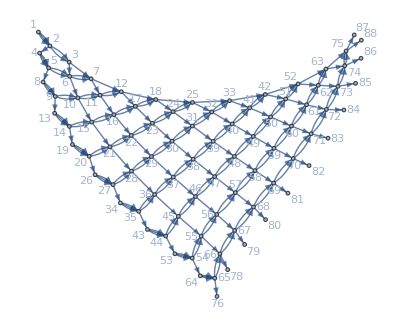

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Most /@ Rest@Position[prepIC[IC2D1],List]
```

{{1,1},{1,2},{1,3,1},{1,4}}

```mathematica
{{Vertex #, , , ((i-1)^2+5(i-1))/2
+0
+1, ((i-1)^2+5(i-1))/2
+1
+1, , ((i-1)^2+5(i-1))/2
+1+1
+(j-1)
+1, , ((i-1)^2+5(i-1))/2
+1+1+(i-1)
+1, , , }, {position, , 1, 1,1, 1,2, 1,3, 1,3,1, , 1,4, , , }, {I-Cat, {, €_(i⊨1)^10[, {1,1,1},, {1,1,i+1},, €_(j⊨1)^(i-1)[, {1,1,i+2}, ],, {i+2,i+3}, ], ], }}, {pos:∑_?^reps (len), , ∑_(i=1)^10 (1+1+i-1+1)
=1/2 (ℕ^2+5 ℕ), , , , , , , , , }, {, , , 1, 1, ∑_j^(i-1) (1)=ℕ=i-1, , , 1, , ↖, }, {, , , , , , 1, ↖, , , , }}
```

```mathematica
∑_(i=1)^ℕ (1+1+i-1+1)
```

1/2 (ℕ^2+5 ℕ)

```mathematica
{$debug=True,RepsLen[IC2D1],$debug=False}[[2]]
```

{1,1,1}: {1,1}

{1,1,1+i}: {1,1}

{1,1,2+i}: {1,1}

€^(-1+i)[{1,1,2+i}]: {-1+i,1}

{2+i,3+i}: {1,1}

€_(i⊨1)^10[{1,1,1},{1,1,1+i},€^(-1+i)[{1,1,2+i}],{2+i,3+i}]: {10,2+i}

{{10,2+i}}

### Figure 5b

```mathematica
IC2b={IndexedConcatenate[{1},{},{n,1,5}]}
```

{€_(n⊨1)^5[{1},{}]}

```mathematica
{{vertex, , , 2(n-1)
+0+1, 2(n-1)
+1+1, , }, {position, , 1, 1,1, 1,1, , }, {I-Cat, {, €_(n⊨1)^5[, {1},, {}, ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^ℕ (1+1)
=2ℕ, , , , }, {, , , 1, 1, ↖, }}
```

```mathematica
Most /@ Rest@Position[prepIC[IC2b],List]
```

{{1,1},{1,2}}

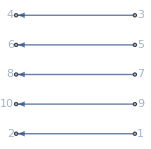

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{$debug=True,RepsLen[IC2b],$debug=False}[[2]]
```

{1}: {1,1}

{}: {1,1}

€_(n⊨1)^5[{1},{}]: {5,2}

{{5,2}}

### Figure 5c

```mathematica
IC2c={IndexedConcatenate[{1,2},{n,1,10}]}
```

{€_(n⊨1)^10[{1,2}]}

```mathematica
Most /@ Rest@Position[prepIC[IC2c],List]
```

{{1,1}}

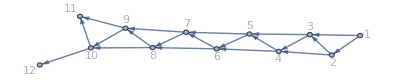

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{vertex, , , 1(n-1)+1, , }, {position, , 1, 1,1, , }, {I-Cat, {, €_(n⊨1)^10[, {1,2}, ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^10 (1)
=ℕ, , , }, {, , , 1:1, ↖, }}
```

```mathematica
{$debug=True,RepsLen[IC2c],$debug=False}[[2]]
```

{1,2}: {1,1}

€_(n⊨1)^10[{1,2}]: {10,1}

{{10,1}}

### Figure 6d

```mathematica
IC2d={IndexedConcatenate[{2,3},{3},{1,2},{m,1,9}]}
```

{€_(m⊨1)^9[{2,3},{3},{1,2}]}

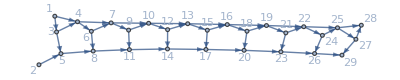

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{vertex, , , 3(m-1)
+0+1, 3(m-1)
+1+1, 3(m-1) 
+2+1, , }, {position, , 1, 1,1, 1,2, 1,3, , }, {I-Cat, {, €_(m⊨1)^9[, {2,3},, {3},, {1,2}, ], }}, {pos:∑_?^reps (len), , 1:∑_(m=1)^ℕ ( 1+1+1)=3ℕ, , , , , }, {, , , 1, 1, 1, ↖, }}
```

```mathematica
Most /@ Rest@Position[prepIC[IC2d],List]
```

{{1,1},{1,2},{1,3}}

### Figure 5e

EDSL representations:

```mathematica
ICNB11={IndexedConcatenate[IndexedConcatenate[{2j-1, 2j}, {j, 1, 3}], IndexedConcatenate[{1, 2}, IndexedConcatenate[{}, 2], 2], 3]};
ICNB10={IndexedConcatenate[IndexedConcatenate[{2j+1, 2j+2}, {j,0,2}], IndexedConcatenate[{1, 2}, IndexedConcatenate[{}, {k,0,1}],{j,0,1}],{i,0,2}]};
Grid[{{ICNB11,Column[Partition[Expand[ICNB11],9]]},{ICNB10,SpanFromAbove}},Spacings->2,Alignment->{{Left,Left},{Center}}]
```

```mathematica
{{{€^3[€_(j⊨1)^3[{2 j-1,2 j}]],€^2[{1,2},€^2[{}]]]}, {{{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}}, {{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}}, {{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}}}}, {{€_(i⊨0)^2[€_(j⊨0)^2[{1+2 j,2+2 j}],€_(j⊨0)^1[{1,2},€_(k⊨0)^1[{}]]]}, }}
```

```mathematica
{{Vertex #, , , , 12((i-1)+1)
+((j-1)+1)
+1, , , 12((i-1)+1)
+3
+3((j-1)+1)
+1, , 12((i-1)+1)
+3
+3((j-1)+1)
+1
 +((k-1)+1)
+1, , , , }, {position, , 1, 1,1, 1,1,1, , 1,2, 1,2,1, 1,2,2, 1,2,2,1, , , , }, {I-Cat, {, €_(i⊨0)^2[, €_(j⊨0)^2[, {2 j-1,2 j}, ],, €_(j⊨0)^1[, {1,2},, €_(k⊨0)^1[, {}, ], ], ], }}, {pos:∑_?^reps (len), , ∑_(i=0)^ℕ ( 3+9)
=12(ℕ+1), , , , , , , , , , , }, {, , , ∑_(j=0)^ℕ (1)
=ℕ+1
=3, , , ∑_(j=0)^ℕ (1+2)
=3(ℕ+1)
=9, , , , , , ↖, }, {, , , , 1, ↖, , 1, ∑_(k=0)^ℕ 1
=ℕ+1
=2, , , ↖, , }, {, , , , , , , , , 1, ↖, , , }}
```

```mathematica
{{Vertex #, , , , 12(i-1)
+(j-1)
+1, , , 12(i-1)
+3
+3(j-1)
+1, , 12(i-1)
+3
+3(j-1)
+1
 +(k-1)
+1, , , , }, {position, , 1, 1,1, 1,1,1, , 1,2, 1,2,1, 1,2,2, 1,2,2,1, , , , }, {I-Cat, {, €_(i⊨1)^3[, €_(j⊨1)^3[, {2 j-1,2 j}, ],, €_(j⊨1)^2[, {1,2},, €_(k⊨1)^2[, {}, ], ], ], }}, {pos:∑_?^reps (len), , ∑_(i=1)^ℕ ( 3+9)
=12ℕ), , , , , , , , , , , }, {, , , ∑_(j=1)^ℕ (1)
=ℕ=3, , , ∑_(j=1)^ℕ (1+2)
=3ℕ=9, , , , , , ↖, }, {, , , , 1, ↖, , 1, ∑_(k=1)^ℕ 1
=ℕ=2, , , ↖, , }, {, , , , , , , , , 1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[ICNB11],$debug=False}[[2]]
```

{-1+2 j,2 j}: {1,1}

€_(j⊨1)^3[{-1+2 j,2 j}]: {3,1}

{1,2}: {1,1}

{}: {1,1}

€^2[{}]: {2,1}

€^2[{1,2},€^2[{}]]: {2,3}

€^3[€_(j⊨1)^3[{-1+2 j,2 j}],€^2[{1,2},€^2[{}]]]: {3,9}

{{3,9}}

#### Musings

There are 9 edge difference sets in each row of the EDSL — for each “i” in the outer I-Cat, but they describe 10 edges, given below:

```mathematica
Grid[Riffle[#,","]& /@ Partition[FromNetDifferenceSets[ExpandAll[ICNB11]],10]]
```

1→2 | , | 1→3 | , | 2→5 | , | 2→6 | , | 3→8 | , | 3→9 | , | 4→5 | , | 4→6 | , | 7→8 | , | 7→9
10→11 | , | 10→12 | , | 11→14 | , | 11→15 | , | 12→17 | , | 12→18 | , | 13→14 | , | 13→15 | , | 16→17 | , | 16→18
19→20 | , | 19→21 | , | 20→23 | , | 20→24 | , | 21→26 | , | 21→27 | , | 22→23 | , | 22→24 | , | 25→26 | , | 25→27

The lengths of the internal ICs are 3×1=3, 2×(1+2×1)=6 , and 2×1=2.  The 9 comes from adding up the lengths of the ICs at the second level, that is, 3×1 + 2×(1+2×1)=3+2×3=3+6=9 elements

There is only 1 edge difference set inside the first “j” I-Cat, and 3 inside the second. In the following, 
(9i+j) comes from the 9 EDSs in the outer I-Cat and the 1 in the first “j” I-Cat;
(9i+3+3j) ”      ”        ”   9 EDSs  ”     ”       ”          ” ,   the 3 in order to to pass the first “j” I-Cat entirely, the 3j comes from the 3 EDSs in the 2nd “j” I-Cat. 
The final integer before each “→” is the vertex number in the inner I-Cat: 1.
The parenthesized expressions at the end of each “→” expression come from the EDSL internal expressions, when 0-indexed (2nd form shown above).

```mathematica
ICNB1TranaTemp=
{IndexedConcatenate[
IndexedConcatenate[Association[vertex->(9i+j)+1,EDS->{2 j+1,2 j+2}],{j,0,2}],
IndexedConcatenate[Association[vertex->(9i+3+3j)+1,EDS->{1,2}],{j,0,1}],
{i,0,2}
]}
```

```mathematica
ICNB1Trana=
{IndexedConcatenate[
IndexedConcatenate[(9i+j)+1->(9i+j)+1+(2j+1),(9i+j)+1->(9i+j)+1+(2j+2),{j,0,2}],
IndexedConcatenate[(9i+3+3j)+1->(9i+3+3j)+1+(1),(9i+3+3j)+1->(9i+3+3j)+1+(2),{j,0,1}],
{i,0,2}
]}
```

{€_(i⊨0)^2[€_(j⊨0)^2[1+9 i+j→2+9 i+3 j,1+9 i+j→3+9 i+3 j],€_(j⊨0)^1[4+9 i+3 j→5+9 i+3 j,4+9 i+3 j→6+9 i+3 j]]}

{€_(i⊨0)^2[€_(j⊨0)^2[(9i+j)+1->(9i+j)+1+(2j+1),(9i+j)+1->(9i+j)+1+(2j+2),],€_(j⊨0)^1[(9i+3+3j)+1->(9i+3+3j)+1+(1),(9i+3+3j)+1->(9i+3+3j)+1+(2)]]}

```mathematica
ExpandAll[ICNB1Trana]
```

{1→2,1→3,2→5,2→6,3→8,3→9,4→5,4→6,7→8,7→9,10→11,10→12,11→14,11→15,12→17,12→18,13→14,13→15,16→17,16→18,19→20,19→21,20→23,20→24,21→26,21→27,22→23,22→24,25→26,25→27}

```mathematica
FromNetDifferenceSets@ExpandAll[ICNB11]
```

{1→2,1→3,2→5,2→6,3→8,3→9,4→5,4→6,7→8,7→9,10→11,10→12,11→14,11→15,12→17,12→18,13→14,13→15,16→17,16→18,19→20,19→21,20→23,20→24,21→26,21→27,22→23,22→24,25→26,25→27}

```mathematica
%133==%134
```

True

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

What we need is  the # reps (number of repetitions) and length (of the argument list for each Indexed Concatenation object.  Suppose for convenience we put the nested ICat in a table (using Insert => Table):

□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □

Then we copy the various parts in, leaving room for the reps & length information, using Ctrl-, to add more columns, if needed. (DEL deletes rows or columns):

I-Cat: | { | €_(i⊨0)^2[ | €_(j⊨0)^2[ | {2 j+1,2 j+2} | ] | , | €_(j⊨0)^1[ | {1,2} | , | €_(k⊨0)^1[ | {} | ] | ] | }
reps: | / | 3 | 3 | 1 | / | / | 2 | 1 | / | 2 | 1 | / | / | /
length: | / | □ | □ | 1 | □ | □ | □ | 1 | / | □ | 1 | / | / | /

Parts filled in from:

{€_(i⊨0)^2[€_(j⊨0)^2[{2 j+1,2 j+2}],€_(j⊨0)^1[{1,2},€_(k⊨0)^1[{}]]]}

All sets of integers count as reps = 1, length = 1.  (length > 1 would include multiple sets inside the I-Cat brackets.)

Now we start to work from the inside out to find the lengths of the I-Cats themselves.  If the contents is fixed, that’s just adding up the reps × length of what’s inside:

I-Cat: | { | €_(i⊨0)^2[ | €_(j⊨0)^2[ | {2 j+1,2 j+2} | ] | , | €_(j⊨0)^1[ | {1,2} | , | €_(k⊨0)^1[ | {} | ] | ] | }
reps: | / | 3 | 3 | 1 | / | / | 2 | 1 | / | 2 | 1 | / | / | /
length: | / | 9=(3×1)+(2×3) | 1 | 1 | / | / | 3=(1×1)+(2×1) | 1 | / | 1=(1×1) | 1 | / | / | /

```mathematica
{{Vertex #, , , , , , , , , }, {I-Cat, {, €_(i⊨0)^2[, €_(j⊨0)^2[, {2 j+1,2 j+2}, ], ,, □, ], }}, {pos:∑_?^reps (len), , 1:∑_(i=0)^2 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

So we get the reps & length for the 4 ICats above: {3,9}, {3,1}, {2,3}, and {2,1} respectively.

### Figure 5f

```mathematica
ICNB2={IndexedConcatenate[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3},4]}
```

{€^4[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3}]}

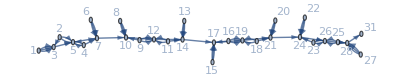

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^5 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[ICNB2],$debug=False}[[2]]
```

{2,2,2}: {1,1}

{1,3,3}: {1,1}

{2}: {1,1}

{1,1,3}: {1,1}

{2}: {1,1}

{1,1,1}: {1,1}

{3}: {1,1}

€^4[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3}]: {4,7}

{{4,7}}

### Figure 5g

```mathematica
ICNB3={IndexedConcatenate[{2, 3}, {1, 2}, {}, 8]}
```

{€^8[{2,3},{1,2},{}]}

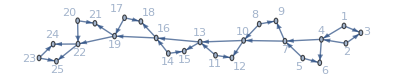

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^5 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[ICNB3],$debug=False}[[2]]
```

{2,3}: {1,1}

{1,2}: {1,1}

{}: {1,1}

€^8[{2,3},{1,2},{}]: {8,3}

{{8,3}}

### Figure 5h

```mathematica
ICNB4={IndexedConcatenate[{1, 6, 8}, {}, {IndexedConcatenate[2,4]}, IndexedConcatenate[{1, IndexedConcatenate[3,3]}, {}, 2], 7]}
```

{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}

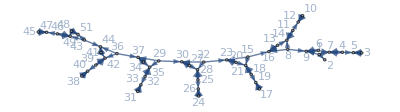

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^5 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[ICNB4],$debug=False}[[2]]
```

{1,6,8}: {1,1}

{}: {1,1}

{€^4[2]}: {1,1}

{1,€^3[3]}: {1,1}

{}: {1,1}

€^2[{1,€^3[3]},{}]: {2,2}

€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]: {7,7}

{{7,7}}

### Figure 5i

```mathematica
ICB5={IndexedConcatenate[IndexedConcatenate[{1,18-2k},{k,1,7}],IndexedConcatenate[{1,1},{k,8,9}],{n,0,25}]}
```

{€_(n⊨0)^25[€_(k⊨1)^7[{1,18-2 k}],€_(k⊨8)^9[{1,1}]]}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^5 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[ICB5],$debug=False}[[2]]
```

{1,18-2 k}: {1,1}

€_(k⊨1)^7[{1,18-2 k}]: {7,1}

{1,1}: {1,1}

€_(k⊨8)^9[{1,1}]: {2,1}

€_(n⊨0)^25[€_(k⊨1)^7[{1,18-2 k}],€_(k⊨8)^9[{1,1}]]: {26,9}

{{26,9}}

### Figure 5j

```mathematica
ICB6={IndexedConcatenate[IndexedConcatenate[{1,7,8},2],IndexedConcatenate[{1,1,7},2],{7},{},{},13]}
```

{€^13[€^2[{1,7,8}],€^2[{1,1,7}],{7},{},{}]}

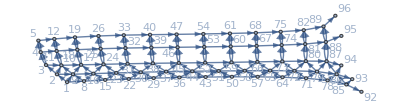

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^5 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[ICB6],$debug=False}[[2]]
```

{1,7,8}: {1,1}

€^2[{1,7,8}]: {2,1}

{1,1,7}: {1,1}

€^2[{1,1,7}]: {2,1}

{7}: {1,1}

{}: {1,1}

{}: {1,1}

€^13[€^2[{1,7,8}],€^2[{1,1,7}],{7},{},{}]: {13,7}

{{13,7}}

### Figure 5k

```mathematica
ICB5b={IndexedConcatenate[IndexedConcatenate[{1,12-2k},{k,1,4}],IndexedConcatenate[{1,1},{k,5,7}],{n,0,18}]}
```

{€_(n⊨0)^18[€_(k⊨1)^4[{1,12-2 k}],€_(k⊨5)^7[{1,1}]]}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^5 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[ICB5b],$debug=False}[[2]]
```

{1,12-2 k}: {1,1}

€_(k⊨1)^4[{1,12-2 k}]: {4,1}

{1,1}: {1,1}

€_(k⊨5)^7[{1,1}]: {3,1}

€_(n⊨0)^18[€_(k⊨1)^4[{1,12-2 k}],€_(k⊨5)^7[{1,1}]]: {19,7}

{{19,7}}

### Figure 6a

```mathematica
IC2D1={IndexedConcatenate[{1,1,1},{1,1,1+i},IndexedConcatenate[{1,1,2+i},-1+i],{2+i,3+i},{i,1,10}]}
```

{€_(i⊨1)^10[{1,1,1},{1,1,1+i},€^(-1+i)[{1,1,2+i}],{2+i,3+i}]}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^5 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[IC2D1],$debug=False}[[2]]
```

{1,1,1}: {1,1}

{1,1,1+i}: {1,1}

{1,1,2+i}: {1,1}

€^(-1+i)[{1,1,2+i}]: {-1+i,1}

{2+i,3+i}: {1,1}

€_(i⊨1)^10[{1,1,1},{1,1,1+i},€^(-1+i)[{1,1,2+i}],{2+i,3+i}]: {10,2+i}

{{10,2+i}}

### Figure 6b

```mathematica
IC2D2={IndexedConcatenate[{-1+2 k,1+2 k},IndexedConcatenate[{1,1},{1,2 k},k],{k,1,12}]}
```

{€_(k⊨1)^12[{-1+2 k,1+2 k},€^k[{1,1},{1,2 k}]]}

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^5 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[IC2D2],$debug=False}[[2]]
```

{-1+2 k,1+2 k}: {1,1}

{1,1}: {1,1}

{1,2 k}: {1,1}

€^k[{1,1},{1,2 k}]: {k,2}

€_(k⊨1)^12[{-1+2 k,1+2 k},€^k[{1,1},{1,2 k}]]: {12,1+2 k}

{{12,1+2 k}}

### Figure 6c

```mathematica
IC2D4={IndexedConcatenate[IndexedConcatenate[{},{1,1,2,2k},k-1],{},{2k,2(1+k)},{k,1,8}]}
```

{€_(k⊨1)^8[€^(-1+k)[{},{1,1,2,2 k}],{},{2 k,2 (1+k)}]}

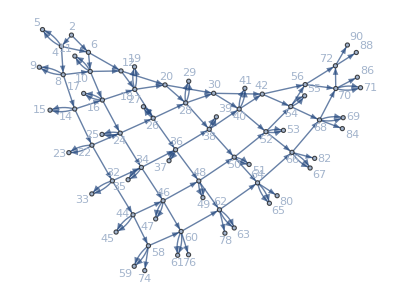

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^5 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[IC2D4],$debug=False}[[2]]
```

{}: {1,1}

{1,1,2,2 k}: {1,1}

€^(-1+k)[{},{1,1,2,2 k}]: {-1+k,2}

{}: {1,1}

{2 k,2 (1+k)}: {1,1}

€_(k⊨1)^8[€^(-1+k)[{},{1,1,2,2 k}],{},{2 k,2 (1+k)}]: {8,2+2 (-1+k)}

{{8,2+2 (-1+k)}}

```mathematica
IC2D4a={IndexedConcatenate[IndexedConcatenate[{},{1,1,2,2k},{j,1,k-1}],{},{2k,2(1+k)},{k,1,8}]}
```

{€_(k⊨1)^8[€_(j⊨1)^(-1+k)[{},{1,1,2,2 k}],{},{2 k,2 (1+k)}]}

### Figure 6e

```mathematica
IC2c={IndexedConcatenate[IndexedConcatenate[{k,k+1},k],{k,1,9}]}
```

{€_(k⊨1)^9[€^k[{k,1+k}]]}

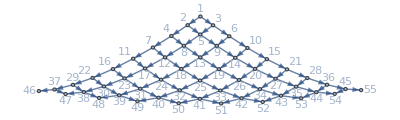

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{I-Cat, {, □, □, □, □, □, □, □, □, □, □, □, □, ], }}, {reps(len), , (), , , , , , , , , , , , , }, {, , , (), (), , , , , , ( ), , , ( ), ↖, }, {, , , , , ()(), , , (), ↖, , ( ), ↖, , , }, {, , , , , , (), ↖, , , , , , , , }}
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, , , , }, {I-Cat, {, €_(n⊨1)^5, €_(i⊨1)^n[, €_(j⊨1)^i[, {z=1/2 n (1+n),i+z,1+i+z}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(n=1)^5 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , , , , }, {, , , 1:∑_(i=1)^n (i)=(n(n+1))/2, , , , , ↖, }, {, , , , 1: ∑_(j=1)^i ( 1)=i, , , ↖, , }, {, , , , , 1:∑^1 1=1, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[IC2c],$debug=False}[[2]]
```

{k,1+k}: {1,1}

€^k[{k,1+k}]: {k,1}

€_(k⊨1)^9[€^k[{k,1+k}]]: {9,k}

{{9,k}}

### Figure 6f

```mathematica
IC2j={IndexedConcatenate[{-1 + 2^k, 2^k, 1 + 2^k}, IndexedConcatenate[{1 + 2^k}, 1 + 2^k], {1}, 
 IndexedConcatenate[{1, -1 + 2^k + j, 2^k + j}, {j, 1, -1 + 2^k}], {k, 1, 10}]}
```

{€_(k⊨1)^10[{-1+2^k,2^k,1+2^k},€^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]]}

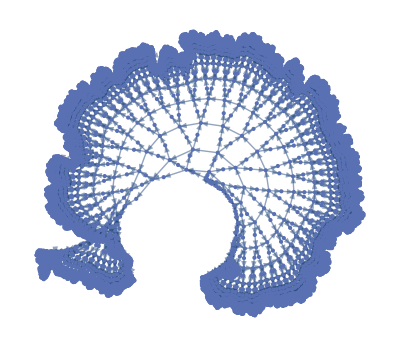

```mathematica
Graph[FromNetDifferenceSets[ExpandAll[%]],VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{{Vertex #, , , , , ((n-1)((n-1)+1) ((n-1)+2))/6+((i-1)((i-1)+1))/2+(j-1)+1, □, □, □, □, , , , }, {I-Cat, {, €_(k⊨1)^10[, {-1+2^k,2^k,1+2^k},, €^(1+2^k)[, {1+2^k}, ],, {1},, €_(j⊨1)^(-1+2^k)[, {1,-1+2^k+j,2^k+j}, ], ], ], }}, {pos:∑_?^reps (len), , 1:∑_(k=1)^10 ( (n(n+1))/2)=(ℕ (ℕ+1) (ℕ+2))/6, , , , □, □, □, □, , , , }, {, , , 1:∑^1 1=1, 2: ∑_^(1+2^k) ( 1)=1+2^k, , □, 1:∑^1 1=1, □, □, , , ↖, }, {, , , , , 1:∑^1 1=1, □, □, □, □, , ↖, , }, {, , , , , , □, , □, □, ↖, , , }}
```

```mathematica
{$debug=True,RepsLen[IC2j],$debug=False}[[2]]
```

{-1+2^k,2^k,1+2^k}: {1,1}

{1+2^k}: {1,1}

€^(1+2^k)[{1+2^k}]: {1+2^k,1}

{1}: {1,1}

{1,-1+2^k+j,2^k+j}: {1,1}

€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]: {-1+2^k,1}

€_(k⊨1)^10[{-1+2^k,2^k,1+2^k},€^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]]: {10,2+2^(1+k)}

{{10,2+2^(1+k)}}

## Trying again

### Example 1

```mathematica
{{I-Cat, reps, len, reps, len}, {{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}, 1, 1, 1, 1}, {{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}, , , 2, 2}, {{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}, , , 7, 7}, {{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}, , , 1, 49}}
```

```mathematica
{{I-Cat, {, €_(k⊨0)^6[, {1,6,8},, {},, {€^4[2]},, €_(j⊨0)^1[, {1,€^3[3]},, {}, ], ], }}, {raw v #, , , 1, 2, 3, , 4, 5, , , }, {v #, , , 7k+1, 7k+2, 7k+3, , 7k+2j+4, 7k+2j+5, , , }, {reps, , 7, 1, 1, 1, 2, 1, 1, , , }, {len, , 7, 1, 1, 1, 2, 1, 1, , , }}
```

This looks helpful. The lists (and ONLY the lists) each receive a raw vertex number: 1, 2, 3, 4, 5. To these are added 7k (for the lists inside the outer I-Cat) or 7k + 2j (for the lists inside the k- and the j- I-Cat.  The len & reps have to be found recursively, which pretty well requires all lists to have reps = 1 and len = 1, but then the vertex number is the (raw v #) + len * (I-Cat Index), with the additional term included for all I-Cats bracketing the given list. We will replace each list l by Rule[vertex number -> vertex number + #]& /@ l, to rebuild the edges of the graph inside the nested I-Cat object.

```mathematica
myICatObj={€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]};
```

```mathematica
Position[myICatObj,List]
```

{{0},{1,1,0},{1,2,0},{1,3,0},{1,4,1,0},{1,4,2,0}}

```mathematica
Most /@ Rest[Position[myICatObj,List]]
```

{{1,1},{1,2},{1,3},{1,4,1},{1,4,2}}

```mathematica
myICatObj[[1]]
```

€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]

```mathematica
myICatObj[[1,4]]
```

€^2[{1,€^3[3]},{}]

### Example 2

```mathematica
pentagraph={IndexedConcatenate[
{1,5n+4,5n+5},
IndexedConcatenate[
IndexedConcatenate[{1},{i,1,n}],
{1,5n+5+k},
{k,1,4}],
IndexedConcatenate[{1},{j,1,n-1}],
{},
{n,1,8}]};
Graph3D[FromNetDifferenceSets[ExpandAll[pentagraph]]]
```

-Graphics3D-

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

```mathematica
{{I-Cat, {, €_(n⊨0)^7[, {1,5 n+4,5 n+5},, €_(k⊨0)^3[, €_(i⊨0)^(n-1)[, {1}, ],, {1,k+5 n+5}, ],, €_(j⊨0)^(n-2)[, {1}, ],, {}, ], }}, {raw v #, , , 1, , , 2, , 3, , , 4, , 5, , }, {raw v # 
T2, , , 1, , , 2, , 2+n, , , 2+4(n+1)
=4n+6, , (4n+6)+(n-1)
=5n+5, , }, {v #, , , (5n+5)n
+1, , , (5n+5)n
+(n+1)k
+1i
+2, , (5n+5)n
+(n+1)k
+1n
+3
 (or maybe 0|1?), , , (5n+5)n
+(n+1)4
+4
(or maybe 0|1?), , (5n+5)n
+(n+1)4
+1(n-1)
+5
(or maybe 0|1?), , }, {reps, , 8, 1, 4, n, 1, , 1, , n-1, 1, , 1, , }, {len, , 5n+5, 1, n+1, 1, 1, , 1, , 1, 1, , 1, , }, {reps×len, , 40(n+1), 1, 4(n+1), n, 1, , 1, , n-1, 1, , 1, , □}}
```

```mathematica
{$debug=True,RepsLen[pentagraph],$debug=False}[[2]]
```

{1,4+5 n,5+5 n}: {1,1}

{1}: {1,1}

€_(i⊨1)^n[{1}]: {n,1}

{1,5+k+5 n}: {1,1}

€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,5+k+5 n}]: {4,1+n}

{1}: {1,1}

€_(j⊨1)^(-1+n)[{1}]: {-1+n,1}

{}: {1,1}

€_(n⊨1)^8[{1,4+5 n,5+5 n},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,5+k+5 n}],€_(j⊨1)^(-1+n)[{1}],{}]: {8,1+n+4 (1+n)}

{{8,1+n+4 (1+n)}}

I feel the need to add the terms in orange to any terms that follow a completed I-Cat, and then maybe the raw v # that follows needs to reset to 0 or 1. I can’t quite work it out without trying cases: n=0, k=0, but we’ve had all n of the len 1 entries in the innermost I-Cat, so that vertex shouldn’t be +3, it should be  + 1 + 1n + 1 (still with the (5n+5)n+(n+1)k in front of that. I think the reason this didn’t show up in the first example is that no I-Cats completed until after the last list, but here we complete two different I-Cats and go on. The +3 was assuming 2 completed lists of len 1 each, but actually we had n+1. Does thing give a rule for continuing?

```mathematica
Most /@ Rest[Position[prepIC[pentagraph],List]]
```

{{1,1},{1,2,1,1},{1,2,2},{1,3,1},{1,4}}

```mathematica
pentagraph
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

```mathematica
pentagraph[[1]]
```

€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]

```mathematica
pentagraph[[1,2]]
```

€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}]

```mathematica
pentagraph[[1,2,1]]
```

€_(i⊨1)^n[{1}]

```mathematica
pentagraph[[1,3]]
```

€_(j⊨1)^(n-1)[{1}]

```mathematica
pentagraph
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

```mathematica
{{I-Cat, {, €_(n⊨1)^8[, {1,5 n+4,5 n+5},, €_(k⊨1)^4[, €_(i⊨1)^n[, {1}, ],, {1,k+5 n+5}, ],, €_(j⊨1)^(n-1)[, {1}, ],, {}, ], }}, {Position, , , 1, , , 1, , 1, , , 1, , 1, , }, {, , , 1, , , 2, , 2, , , 3, , 4, , }, {, , , , , , 1, , 2, , , 1, , , , }, {, , , , , , 1, , , , , , , , , }, {raw v # 
T3, , , 1, , , 1+1
=2, , 2+n
=n+2, , , 2+4(n+1)
=4n+6, , (4n+6)+(n-1)
=5n+5, , }, {v #, , , (5n+5)(n-1)
+1, , , (5n+5)(n-1)
+(n+1)(k-1)
+1(i-1)
+2, , (5n+5)(n-1)
+(n+1)(k-1)
+1n
+2, , , (5n+5)(n-1)
+(n+1)4
+(n-1)(j-1)
+2, , (5n+5)(n-1)
+(n+1)4+(n-1)1

+2, , }, {reps, , 8, 1, 4, n, 1, , 1, , n-1, 1, , 1, , }, {len, , 5n+5, 1, n+1, 1, 1, , 1, , 1, 1, , 1, , }, {reps×len, , 40(n+1), 1, 4(n+1), n, 1, , 1, , n-1, 1, , 1, , }}
```

This must be checked with small values of n, k, i.

```mathematica
{(5n+5)(n-1)+1,(5n+5)(n-1)+(n+1)(k-1)+1(i-1)+2,
(5n+5)(n-1)+(n+1)(k-1)+1n+2,
(5n+5)(n-1)+(n+1)4+(n-1)(j-1)+2,
(5n+5)(n-1)+(n+1)4+1(n-1)+2}/.n->1/.k->4/.i->1/.j->1
```

{1,8,9,10,10}

Need more examples.

```mathematica
pentagraph
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,k+5 n+5}],€_(j⊨1)^(n-1)[{1}],{}]}

```mathematica
pentagraph//InputForm
```

```mathematica
{IndexedConcatenate[{1, 4 + 5*n, 5 + 5*n}, 
  IndexedConcatenate[IndexedConcatenate[{1}, {i, 0, n-1}], 
   {1, 6 + k + 5*n}, {k, 0, 3}], IndexedConcatenate[{1}, 
   {j, 0, -2 + n}], {}, {n, 1, 8}]}
```

{€_(n⊨1)^8[{1,5 n+4,5 n+5},€_(k⊨0)^3[€_(i⊨0)^(n-1)[{1}],{1,k+5 n+6}],€_(j⊨0)^(n-2)[{1}],{}]}

```mathematica
{IndexedConcatenate[{1, 9 + 5*n, 10 + 5*n}, 
  IndexedConcatenate[IndexedConcatenate[{1}, {i, 0, n}], 
   {1, 11 + k + 5*n}, {k, 0, 3}], IndexedConcatenate[{1}, 
   {j, 0, -1 + n}], {}, {n, 0, 7}]}
```

{€_(n⊨0)^7[{1,5 n+9,5 n+10},€_(k⊨0)^3[€_(i⊨0)^n[{1}],{1,k+5 n+11}],€_(j⊨0)^(n-1)[{1}],{}]}

```mathematica
ExpandAll[%183]==ExpandAll[pentagraph]
```

True

## Improved format for noting reps & len

Record reps & len in the format: reps(len)

For all lists in curly braces, reps(len) = 1(1).
For I-Cats use the iterator to calculate reps. (For iterator = {var,start,stop} or “var=start ... stop”, reps = stop - start + 1.) Temporarily leave len blank: reps( )

Everything inside an I-Cat is recorded one line down from the I-Cat itself. At the final closing bracket, add up all reps(len) entries since the beginning of the I-Cat, and put this sum in as the len.

In this example, color coding has been added to show which entries were added, and the sum (the len of the I-Cat) found:

```mathematica
{{I-Cat, {, €_(n⊨0)^7[, {1,5 n+9,5 n+10},, €_(k⊨0)^3[, €_(i⊨0)^n[, {1}, ],, {1,k+5 n+11}, ],, €_(j⊨0)^(n-1)[, {1}, ],, {}, ], }}, {reps(len), , 8(5(n+2)), , , , , , , , , , , , , }, {, , , 1(1), 4(n+2), , , , , , n(1), , , 1(1), ↖, }, {, , , , , (n+1)(1), , , 1(1), ↖, , 1(1), ↖, , , }, {, , , , , , 1(1), ↖, , , , , , , , }}
```

```mathematica
RepsLen[pentagraph]
```

{1,4+5 n,5+5 n}: {1,1}

{1}: {1,1}

€_(i⊨1)^n[{1}]: {n,1}

{1,5+k+5 n}: {1,1}

€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,5+k+5 n}]: {4,1+n}

{1}: {1,1}

€_(j⊨1)^(-1+n)[{1}]: {-1+n,1}

{}: {1,1}

€_(n⊨1)^8[{1,4+5 n,5+5 n},€_(k⊨1)^4[€_(i⊨1)^n[{1}],{1,5+k+5 n}],€_(j⊨1)^(-1+n)[{1}],{}]: {8,1+n+4 (1+n)}

{{8,1+n+4 (1+n)}}

Adding in rows with the Position of Lists information, and calculated raw vertex numbers and (complete) vertex numbers:

```mathematica
{{I-Cat, {, €_(n⊨0)^7[, {1,5 n+9,5 n+10},, €_(k⊨0)^3[, €_(i⊨0)^n[, {1}, ],, {1,k+5 n+11}, ],, €_(j⊨0)^(n-1)[, {1}, ],, {}, ], }}, {Position, , , 1, , , 1, , 1, , , 1, , 1, , }, {, , , 1, , , 2, , 2, , , 3, , 4, , }, {, , , , , , 1, , 2, , , 1, , , , }, {, , , , , , 1, , , , , , , , , }, {raw v # 
T3, , , 1, , , 1+1
=2, , 2+(n+1)
=n+3, , , 2+4(n+2)
=4n+4, , (4n+4)+(n)
=5n+4, , }, {v #, , , n(5(n+2))
+(1), , , n(5(n+2))
+k(n+2)
+i(1)
+(2), , n(5(n+2))
+k(n+2)
+(n+1)(1)
+(n+3), , , n(5(n+2))
+4(n+2)
+j(1)
+(4n+4), , n(5(n+2))
+n(n+2)
+n(1)
+(5n+4), , }, {reps(len), , 8(5(n+2)), , , , , , , , , , , , , }, {, , , 1(1), 4(n+2), , , , , , n(1), , , 1(1), ↖, }, {, , , , , (n+1)(1), , , 1(1), ↖, , 1(1), ↖, , , }, {, , , , , , 1(1), ↖, , , , , , , , }}
```

Whenever inside an I-Cat, there is a “var(len)” term added. After we exit from an I-Cat but remain on the same level, add “reps(len)” for the I-Cat. The latter are the entries shown in orange in the v # row.